# MOL : Finite Difference Method

### functions

#### options settings

```mathematica
SetDirectory["/home/julian/mathematica/ecsf_new_trial"];
ClearSystemCache[];
Needs["Splines`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

```mathematica
SetOptions[Interpolation, InterpolationOrder -> 4, PeriodicInterpolation -> True];
Options[Interpolation]
```

{InterpolationOrder→4,PeriodicInterpolation→True}

```mathematica
SetOptions[NIntegrate, MaxRecursion -> 20];
Options[NIntegrate, MaxRecursion]
```

{MaxRecursion→20}

```mathematica
SetOptions[NDSolve`FiniteDifferenceDerivative, DifferenceOrder -> 6, PeriodicInterpolation -> True];
Options[NDSolve`FiniteDifferenceDerivative]
```

{DifferenceOrder→6,PeriodicInterpolation→True}

```mathematica
SetOptions[NDSolve, MaxSteps -> 15000];
Options[NDSolve, {MaxSteps, InterpolationOrder}]
```

{MaxSteps→15000,InterpolationOrder→Automatic}

```mathematica
SetOptions[NDSolve`ProcessEquations, MaxSteps -> 15000];
Options[NDSolve`ProcessEquations, MaxSteps]
```

{MaxSteps→15000}

#### curve generator

```mathematica
Clear[pcg,rpcg];
pcg[num_,xy__List]:=
Module[{pts,n,spline,
fpts=50,order=8,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,xfitdat,yfitdat,
initialcurve,area,length,centroid},

pts=xy;
n=Length[pts];
pts=Append[pts,First[pts]];
pts=Join[{pts[[-3]],pts[[-2]]},pts,{pts[[2]],pts[[3]]}];
spline=SplineFit[pts,Cubic];

xpts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[1]]},{i,0,fpts}];
ypts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[2]]},{i,0,fpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
initialcurve[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

 area=1/2 
NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,0,2π}
];
length=NIntegrate[Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π}];
centroid=1/length 
NIntegrate[initialcurve[u] Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π},AccuracyGoal->9];

Subscript[curve, num][u_]:=10Sqrt[2π/area](initialcurve[u]-centroid);
Subscript[inilen, num]=10Sqrt[2π/area]length;

Show[
ListPlot[10Sqrt[2π/area]Table[xy[[i]]-centroid,{i,1,n}],PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[Subscript[curve, num][2Pi i/100],{i,0,100}],AspectRatio->Full],
ParametricPlot[Subscript[curve, num][u],{u,0,2Pi}]]

];


rpcg[num_,xy__List]:=
Module[{pts,n,spline,
fpts=50,order=8,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,xfitdat,yfitdat,
initialcurve,area,length,centroid,curve},

pts=xy;
n=Length[pts];
pts=Append[pts,First[pts]];
pts=Join[{pts[[-3]],pts[[-2]]},pts,{pts[[2]],pts[[3]]}];
spline=SplineFit[pts,Cubic];

xpts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[1]]},{i,0,fpts}];
ypts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[2]]},{i,0,fpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
initialcurve[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

 area=1/2 
NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,0,2π}
];
length=NIntegrate[Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π}];
centroid=1/length 
NIntegrate[initialcurve[u] Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π},AccuracyGoal->9];

Subscript[curve, num][u_]:=10Sqrt[2π/area](initialcurve[u]-centroid);

Print[
TableForm[{{
ParametricPlot[spline[u],{u,0,Length[pts]}],
Show[
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[spline[2+(n)i/100],{i,0,100}]],
ParametricPlot[spline[u],{u,2,2+n}]],
Show[
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full,Axes->False],
ListPlot[Table[initialcurve[2Pi i/100],{i,0,100}]],
ParametricPlot[initialcurve[u],{u,0,2Pi}],
Graphics[{Green,PointSize[Medium],Point[centroid]}]],
Show[
ListPlot[10Sqrt[2π/area]Table[xy[[i]]-centroid,{i,1,n}],PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[Subscript[curve, num][2Pi i/100],{i,0,100}],AspectRatio->Full],
ParametricPlot[Subscript[curve, num][u],{u,0,2Pi}]]
}}]
];
]
```

#### plotting

```mathematica
Clear[lineplot3d,erplot,evoplot3d,cenplot,cenplot3d,multicenplot3d,meancenplot,meancenplot3d];

lineplot3d[sol_List,scale_:1,opts___]:=
Module[{plots,n,t1,t2},

n=Length[sol]/2-1;
{t1,t2}=First[First[sol][[2]]][[1]];
If[t2≤99&&t2>1,t2=t2-1];

plots=Table[{scale  Subscript[x, i][t]/.sol[[i+1]],scale  Subscript[y, i][t]/.sol[[i+n+2]],t},{i,0,n}
];
ParametricPlot3D[plots//Evaluate,{t,t1,t2},AspectRatio->1,PerformanceGoal->"Speed",opts]
];

erplot[sol_List,tt1_:0,tt2_:100]:=
Module[{t1,t2},
{t1,t2}=First[First[sol][[2]]][[1]];
If[tt1>t1,t1=tt1];
If[tt2<t2  ,t2=tt2];
Plot[{error[sol,t]},{t,t1,t2},PerformanceGoal->"Speed"]
];

evoplot3d[num_Integer,scale_:3,opts___]:=
Module[{sol,n,curplot,lineplots},
sol=Subscript[solution, num];
n=Length[sol];

curplot=ParametricPlot3D[
{{scale Subscript[curve, num][u][[1]],scale  Subscript[curve, num][u][[2]],0},{0,0,100}},
{u,0,2π},PlotRange->All,PerformanceGoal->"Speed",opts];
lineplots=Table[lineplot3d[sol[[i]],scale,PlotStyle->{{Black,Thin}}],{i,1,n}];

Show[curplot,lineplots]
];

cenplot[num_,t1_:0,t2_:99.9]:=
ParametricPlot[centroid[num,t],{t,t1,t2},PerformanceGoal->"Speed",PlotRange->Full];

cenplot3d[num_,scale_:10,opts___]:=
Show[
evoplot3d[num,scale,opts],ParametricPlot3D[{scale centroid[num,t][[1]],scale centroid[num,t][[2]],t},{t,0,99.9},PerformanceGoal->"Speed",PlotRange->Full,PlotStyle->{Thick,Red}]
];

multicenplot3d[n_,scale_:3,opts___]:=
Show[
Table[
ParametricPlot3D[Flatten[{scale centroid[i,t],t}],{t,0,99.5},PerformanceGoal->"Speed",MaxRecursion->0,PlotStyle->{Hue[i/n]},opts],{i,1,n}]
];

c2plot[n_,opts___]:=
Plot[{(c[t]/.Subscript[zsol, n][[1]])^2},{t,0,99.9},PlotRange->All,opts];

meancenplot3d[num_]:=
ParametricPlot3D[Flatten[{ meancen[num,t],t/100}],{t,0,99},PlotRange->All,PerformanceGoal->"Speed",MaxRecursion->2];

meancenplot[n_]:=
ParametricPlot[Table[meancen[i,t],{i,1,n}],{t,0,99},PlotRange->All,PerformanceGoal->"Speed",MaxRecursion->1,PlotStyle->{Red,Blue}];
```

#### n points on curve

```mathematica
Clear[curgrdpts];

curgrdpts[num_Integer,n_Integer:150]:=
Block[{pts},
pts=Thread[Subscript[curve, num][2π Range[0,n]/n]];
Table[{2π i/n,pts[[i+1]]},{i,0,n}]
];
```

#### process equation

```mathematica
Clear[proequ];

proequ[t0_:0,icpts_List]:=
Module[{n,grdpts,ugrid,X,Y,xu,xuu,yu,yuu,v,xeqns,yeqns,ic,xic,yic},

n=Length[icpts]-1;
grdpts=Range[0,n];
ugrid=icpts[[All,1]];

X[t_]=Through[Thread[Subscript[x, grdpts]][t]];
Y[t_]=Through[Thread[Subscript[y, grdpts]][t]];

xu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,X[t]];
yu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,Y[t]];
xuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,X[t]];
yuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,Y[t]];
v=Sqrt[xu^2+yu^2];

xeqns = Thread[D[X[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)xu+xuu)];
yeqns = Thread[D[Y[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)yu+yuu)];

ic=Flatten@Table[Thread[{Subscript[x, i][t0],Subscript[y, i][t0]}==icpts[[i+1,2]]],{i,0,n}];

First[
NDSolve`ProcessEquations[
Join[xeqns,yeqns,ic],
Join[Thread[Subscript[x, grdpts]],Thread[Subscript[y, grdpts]]],
t]
]

];
```

#### length & area

```mathematica
Clear[length,area];

length[sol_List,t_]:=
Block[{n,grid,X,Y,fddf},

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

Total[Drop[Sqrt[fddf[X]^2 +fddf[Y]^2],1]]

];

area[sol_List,t_]:=
Block[{n,grid,X,Y,fddf},

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

Total[Drop[fddf[X]Y -fddf[Y]X,1]]/2

];
```

#### pretest

```mathematica
Clear[pretest];
pretest[state_NDSolve`StateData]:=
Block[{sta,t,sol,n,grid,X,Y,fddf},
sta=state;
t=First[state@"CurrentTime"];
NDSolve`Iterate[sta,t];
sol=NDSolve`ProcessSolutions[sta];

n=Length[sol]/2-1;
grid=Range[0,n];
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

1000Abs[
Total[Drop[Y  fddf[X] -X  fddf[Y],1]]/2+2π t -200π
]

]
```

#### error test

```mathematica
error[sol_List,t_]:=
Block[{t1,t2,n,grid,X1,Y1,X,Y,fddf},

{t1,t2}=First[First[sol][[2]]][[1]];
n=Length[sol]/2-1;
grid=Range[0,n];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

X1=Through[Thread[Subscript[x, grid]][t1]]/.sol;
Y1=Through[Thread[Subscript[y, grid]][t1]]/.sol;
X=Through[Thread[Subscript[x, grid]][t]]/.sol;
Y=Through[Thread[Subscript[y, grid]][t]]/.sol;

1000Abs[
(Total[Drop[fddf[X]Y -fddf[Y]X,1]]-Total[Drop[fddf[X1]Y1 -fddf[Y1]X1,1]])/2
+2π( t-t1 )]

];
```

#### cutfit

```mathematica
Clear[cut];

cut[sol_List]:=
Module[{n,t1,t2,grid,X1,Y1,X2,Y2,fddf,
dist,dmin,l1,l2,l,i,j,d,
newdist,nnew,newX,newY,newgrid},

{t1,t2}=First[First[sol][[2]]][[1]]-{0,1};
n=Length[sol]/2-1;
grid=Range[0,n];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

X1=Through[Thread[Subscript[x, grid]][t1]]/.sol;
Y1=Through[Thread[Subscript[y, grid]][t1]]/.sol;
dist=Sqrt[fddf[X1]^2 +fddf[Y1]^2];
l1=Total[Drop[dist,1]];
dmin=1Min@dist;

X2=Through[Thread[Subscript[x, grid]][t2]]/.sol;
Y2=Through[Thread[Subscript[y, grid]][t2]]/.sol;
dist=Sqrt[fddf[X2]^2 +fddf[Y2]^2];
l2=Total[Drop[dist,1]];

newdist=Reap[
For[i=1;j=0,i≤ n,i++,
d=Sum[dist[[m]],{m,j+1,i}];
If[i==n,Sow[{i,d}];Break[],None,Print["Error while fitting: Break at i=n"]];
If[d≥ dmin,j=i;Sow[{i,d}],None,Print["Error while fitting: Sow for d>dmin"]];
];
][[2,1]];
nnew=Length[newdist];

If[l2!=Total[newdist[[All,2]]],Print["Error after fitting: Fitted length unequal original length"];
];
Subscript[l, 0]=0;
Do[Subscript[l, i]=Subscript[l, i-1]+newdist[[i,2]],{i,1,nnew}];

newX=Through[Thread[Subscript[x, newdist[[All,1]]]][t2]]/.sol;
newY=Through[Thread[Subscript[y, newdist[[All,1]]]][t2]]/.sol;
newgrid=Table[{2π Subscript[l, i]/l2,{newX[[i]],newY[[i]]}},{i,1,nnew}];
Prepend[newgrid,{0,Last[newgrid][[2]]}]

]
```

#### fit

```mathematica
Clear[fit];

fit[sol_List]:=
Module[{n,t1,t2,grid,X1,Y1,X2,Y2,fddf,
dist,dmin,l1,l2,l,i,j,d,
newdist,nnew,newX,newY,newgrid,
xmdp,ymdp,order,xexp,yexp,xfk,yfk,xpara,ypara,yfitdat,xfitdat,fc},

{t1,t2}=First[First[sol][[2]]][[1]]-{0,1};
n=Length[sol]/2-1;
grid=Range[0,n];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], grid];

X1=Through[Thread[Subscript[x, grid]][t1]]/.sol;
Y1=Through[Thread[Subscript[y, grid]][t1]]/.sol;
dist=Sqrt[fddf[X1]^2 +fddf[Y1]^2];
l1=Total[Drop[dist,1]];
dmin=1Min@dist;

X2=Through[Thread[Subscript[x, grid]][t2]]/.sol;
Y2=Through[Thread[Subscript[y, grid]][t2]]/.sol;
dist=Sqrt[fddf[X2]^2 +fddf[Y2]^2];
l2=Total[Drop[dist,1]];

newdist=Reap[
For[i=1;j=0,i≤ n,i++,
d=Sum[dist[[m]],{m,j+1,i}];
If[i==n,Sow[{i,d}];Break[],None,Print["Error while fitting: Break at i=n"]];
If[d≥ dmin,j=i;Sow[{i,d}],None,Print["Error while fitting: Sow for d>dmin"]];
];
][[2,1]];
nnew=Length[newdist];

If[l2!=Total[newdist[[All,2]]],Print["Error after fitting: Fitted length unequal original length"];
];
;
Subscript[l, 0]=0;
Do[Subscript[l, i]=Subscript[l, i-1]+newdist[[i,2]],{i,1,nnew}];

newX=Through[Thread[Subscript[x, newdist[[All,1]]]][t2]]/.sol;
newY=Through[Thread[Subscript[y, newdist[[All,1]]]][t2]]/.sol;
newgrid=Table[{2π Subscript[l, i]/l2,{newX[[i]],newY[[i]]}},{i,1,nnew}];
newgrid=Prepend[newgrid,{0,Last[newgrid][[2]]}];

xmdp=Table[{newgrid[[i,1]],newgrid[[i,2,1]]},{i,1,nnew+1}];
ymdp=Table[{newgrid[[i,1]],newgrid[[i,2,2]]},{i,1,nnew+1}];

order=16-IntegerPart[t2/8];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xmdp,xexp[u],xpara ,u];
yfitdat=FindFit[ymdp,yexp[u],ypara ,u];

fc[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};
Print["Fit at time ",t2," Deviation in curve length: ",100(NIntegrate[Sqrt[Evaluate[(D[fc[u], u]).(D[fc[u], u])]],{u,0,2π}]-l2)/l2,
"%"
];

Table[{2π i/ nnew,fc[2π i/nnew]},{i,0,nnew}]
]
```

#### evolution

```mathematica
Clear[evolution];

evolution[num_Integer,n_Integer:150]:=
Module[{grid,state,dt,sol,er,t,tfinal},
Subscript[solution, num]={};

grid=curgrdpts[num,n];
state=proequ[0,grid];
er=pretest[state];
If[er>.5,Return[Print["Pretest failed at t=",0," the error was ",er," (wild curve)"]]];

For[t=0,t<100,t++,
NDSolve`Iterate[state,t];
sol=NDSolve`ProcessSolutions[state];
er=error[sol,t];
If[er>2,
Subscript[solution, num]=Append[Subscript[solution, num],sol];
Block[{t1,t2,newgrid,newstate,newsol,newer},
{t1,t2}=First[First[sol][[2]]][[1]];
newgrid=fit[sol];
newstate=proequ[t2-1,newgrid];
NDSolve`Iterate[newstate,t2];
newsol=NDSolve`ProcessSolutions[newstate];
newer=error[newsol,t2];
If[newer≥ 2,
Print["Error after iteration of fitted state. The error was ",newer, "(",er,") at time ",t2,"(",t2-1,")"];
Abort[];
];
state=newstate;
];
];
];
tfinal=area[sol,99]/(2π)+99;
NDSolve`Iterate[state,tfinal];
sol=NDSolve`ProcessSolutions[state];

Subscript[solution, num]=Append[Subscript[solution, num],sol];
]
```

#### selector (input: solutions & time, output: coords {x,y} according time), picker

```mathematica
Clear[selector,picker];
selector[sol_,t_]:=
Module[{n,ttab,i,grid,X,Y},
n=Length[sol];
ttab=Table[First[First[sol[[i]]][[2]]][[1]][[1]],{i,1,n}];
ttab=Append[ttab,First[First[sol[[n]]][[2]]][[1]][[2]]];
If[t<0||t>ttab[[n+1]],
Print["Error (selector): time value (",t,") lies outside the range of data."];
Abort[];
];
For[i=1,i≤n&&t>ttab[[i+1]],i++
];
grid=Range[0,Length[sol[[i]]]/2 -1];
X=Through[Thread[Subscript[x, grid]][t]]/.sol[[i]];
Y=Through[Thread[Subscript[y, grid]][t]]/.sol[[i]];
{X,Y}
];

picker[sol_,t_]:=
Module[{n,ttab,i,grid,X,Y},
n=Length[sol];
ttab=Table[First[First[sol[[i]]][[2]]][[1]][[1]],{i,1,n}];
ttab=Append[ttab,First[First[sol[[n]]][[2]]][[1]][[2]]];
If[t<0||t>ttab[[n+1]],
Print["Error (selector): time value (",t,") lies outside the range of data."];
Abort[];
];
For[i=1,i≤n&&t>ttab[[i+1]],i++
];
i
]
```

#### centroid

```mathematica
Clear[centroid];
centroid[num_,t_]:=
Module[{X,Y,n,v,l},
{X,Y}=selector[Subscript[solution, num],t];
n=Length@X-1;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n],DifferenceOrder->6];
v=Sqrt[fddf[X]^2 +fddf[Y]^2];
l=Total[Drop[v,1]];

{Total[Drop[X v,1] ],Total[Drop[Y v,1]]}/l

];
```

#### full functions (fufus): area, length, iso, action

```mathematica
Clear[flength,farea,isofit,action];

flength[num_,t_]:=
Module[{sol,i},
sol=Subscript[solution, num];
i=picker[sol,t];
length[sol[[i]],t]
]

farea[num_,t_]:=
Module[{sol,i},
sol=Subscript[solution, num];
i=picker[sol,t];
area[sol[[i]],t]
];

isofit[num_,fitpts_:100,order_:20]:=
Block[{tt=99.9,list,ifi},
list=Append[Table[{tt i/fitpts,flength[num,tt i/fitpts]^2/farea[num,tt i/fitpts]},{i,0,fitpts}],{100,4π}];
Subscript[iso, num][t_]=Fit[list,Thread[t^Range[0,order]],t];
Subscript[l, num][t_]=Sqrt[Subscript[iso, num][t](200π-2π t)];

];

action[n_,num_,t_]:=(Subscript[iso, num][t](1+(c[t]/.Subscript[zsol, n][[1]])/Subscript[l, num][t]));
```

#### pde for c(t)

```mathematica
Clear[zpde];
zpde[n_]:=
Block[{clist=Range[1,n],noc,z,pde,bc,c},
noc=Length[clist];
z[t_]:=Sum[Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])],{num,clist}];
pde=Evaluate[D[z[t], t]] ==0;
bc=Sum[Subscript[l, num][t] Exp[-Subscript[iso, num][0](1+c[t]/Subscript[l, num][t])] /.t->0,{num,clist}]/z[0]==Sum[Subscript[l, num][t]/.t->0,{num,clist}]/noc;
Subscript[co, noc]=c[0]/.FindRoot[bc,{c[0],-290}];
Print["E",noc,": c",noc,"(0)=",Subscript[co, noc]];

Timing[Subscript[zsol, noc]=NDSolve[{pde,c[0]==Subscript[co, noc]},c,{t,0,99.9}]]//Print;
]
```

#### prefactor & exponent fit for c(t)

```mathematica
Clear[c2fit,vtab,ktab];

c2fit[n_Integer,t1_,t2_,pts_:50]:=
Block[{data,expr,pars,cf},
data=Table[{t1 +(t2-t1)i/pts,(c[t1 +(t2-t1)i/pts]/.Subscript[zsol, n][[1]])^2},{i,0,pts}];
expr=k Abs[(100-t)]^v;
pars={{k,400},{v,1}};
cf=FindFit[data,expr,pars,t];
{Sqrt[k],v/2}/.cf
];

vtab[n_Integer,t1_,t2_,int_:10]:=
Quiet[
TableForm[Table[c2fit[i,t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int][[2]],{j,1,int},{i,1,n}],
TableHeadings->{Table[{t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int},{j,1,int}],Table[i,{i,1,n}]}]
];

ktab[n_Integer,t1_,t2_,int_:10]:=
Quiet[
TableForm[Table[c2fit[i,t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int][[1]],{j,1,int},{i,1,n}],
TableHeadings->{Table[{t1+(t2-t1)( j-1)/int,t1+(t2-t1) j/int},{j,1,int}],Table[i,{i,1,n}]}]
]
```

#### mean centroid & variance

```mathematica
Clear[meancen,varcen];
meancen[n_,t_]:=
Sum[centroid[num,t] Exp[-action[n,num,t]],{num,1,n}]/Sum[Exp[-action[n,num,t]],{num,1,n}];

varcen[n_,t_]:=
Sqrt[
Sum[centroid[num,t]^2 Exp[-action[n,num,t]],{num,1,n}]/Sum[Exp[-action[n,num,t]],{num,1,n}]-meancen[n,t]^2
];

varcen2[n_,t_]:=
Sqrt[
Sum[(centroid[num,t]-meancen[n,t])^2 Exp[-action[n,num,t]],{num,1,n}]/Sum[Exp[-action[n,num,t]],{num,1,n}]
];
```

### evolution

#### initial conditions (curves)

```mathematica
pcg[0,{{0,4},{4,0},{0,-4},{-4,0}}];
pcg[1,{{0,4},{4,0},{0,-4},{0,-1},{-1,2},{-2,1},{-1,-1},{-3,-1}}];
pcg[2,{{0,4},{3,3},{2,1},{0,2},{0,0},{4,-1},{0,-4},{-4,0}}];
pcg[3,{{-1,3},{0,3},{1,1},{4,0},{2,-2},{1,-1},{0,-1},{-1,-2},{-4,0},{-3,1},{-3/2,0}}];
pcg[4,{{0,2},{0,4},{2,2},{4,0},{0,-4},{0,-1},{2,-1},{2,0}}];
pcg[5,{{0,1},{2,2},{2,0},{-2,0},{0,-3},{-1,-4},{-2,-2},{-4,0},{-2,4}}];
pcg[6,{{0,1},{2,2},{2,0},{0,-3},{-1,-4},{-2,-2},{-4,-2},{-4,0},{-2,-1}}];
pcg[7,{{0,-1},{2,0},{3,0},{2,-2},{3,-4},{0,-4},{-1,-3},{-4,-2},{-3,0},{-2,1}}];
pcg[8,{{0,1},{4,4},{4,1},{2,0},{3,-2},{0,-3},{-2,-3},{-4,0},{-1,4}}];
pcg[9,{{1,4},{2,2},{4,1},{2,0},{-2,0},{1,-4},{-3,-5},{-4,-8},{-6,-6},{-4,-4},{-4,1},{-2,2}}];
pcg[10,{{-1/4,1/10},{3,2},{2,-1},{0,-1/8},{-4,-1},{-4,4}}];
pcg[11,{{-8,4},{-4,6},{0,8},{2,6},{-5,4},{-4,3},{4,4},{5,0},{2,0},{0,-4},{-2,-3},{1,1},{0,2},{-4,0}}];
pcg[12,{{-3,5},{1,2},{3,3},{4,0},{-2,3},{-3,2},{-5/4,1/2},{-2,-3/2},{-3/2,-2},{0,-2},{0,-4},{-3,-2},{-5,-1},{-5,0},{-4,2}}];
```

#### evolution & isofit

```mathematica
Timing@evolution[0,50]
```

{2.20814,Null}

```mathematica
Timing@evolution[1,200]
```

Fit at time 97. Deviation in curve length: 0.000342441%

{24.1695,Null}

```mathematica
Timing@evolution[2,150]
```

{19.3132,Null}

```mathematica
Timing@evolution[3,170]
```

Fit at time 4. Deviation in curve length: -0.0343826%

Fit at time 91. Deviation in curve length: 0.00228165%

{23.2175,Null}

```mathematica
Timing@evolution[4,150]
```

Fit at time 24. Deviation in curve length: 0.0124969%

Fit at time 98. Deviation in curve length: 0.000450471%

{18.5892,Null}

```mathematica
Timing@evolution[5,200]
```

Fit at time 54. Deviation in curve length: 0.00508591%

{36.0143,Null}

```mathematica
Timing@evolution[6,150]
```

Fit at time 68. Deviation in curve length: 0.00736406%

{23.1774,Null}

```mathematica
Timing@evolution[7,150]
```

Fit at time 11. Deviation in curve length: 0.0195441%

Fit at time 49. Deviation in curve length: -0.00151696%

{21.4013,Null}

```mathematica
Timing@evolution[8,150]
```

Fit at time 21. Deviation in curve length: 0.0250887%

Fit at time 81. Deviation in curve length: 0.00272313%

{20.8493,Null}

```mathematica
Timing@evolution[9,250]
```

Fit at time 32. Deviation in curve length: 0.00478761%

{34.9862,Null}

```mathematica
Timing@evolution[10,250]
```

Fit at time 7. Deviation in curve length: 0.00115855%

Fit at time 36. Deviation in curve length: -0.0419044%

Fit at time 93. Deviation in curve length: -0.00158102%

{51.9032,Null}

```mathematica
Timing@evolution[11,300]
```

Fit at time 5. Deviation in curve length: -0.411308%

Fit at time 13. Deviation in curve length: -0.42999%

Fit at time 24. Deviation in curve length: -0.0212971%

{75.9487,Null}

```mathematica
Timing@evolution[12,300]
```

Fit at time 33. Deviation in curve length: 0.0558487%

Fit at time 84. Deviation in curve length: -0.00108979%

{66.6282,Null}

```mathematica
n=12;
Do[isofit[i],{i,0,n}]
```

```mathematica
Subscript[iso, 1][100]/4/Pi-1
```

-0.000120108

#### export plots

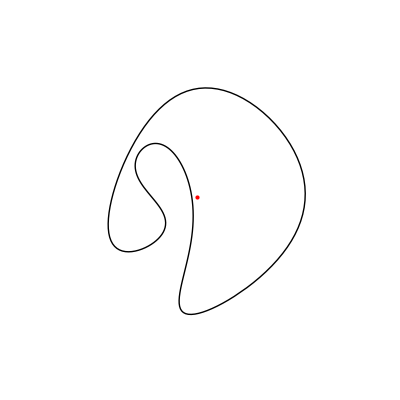
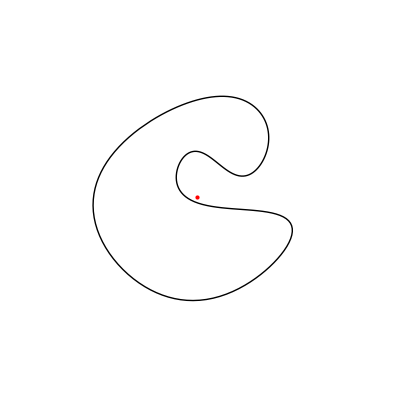
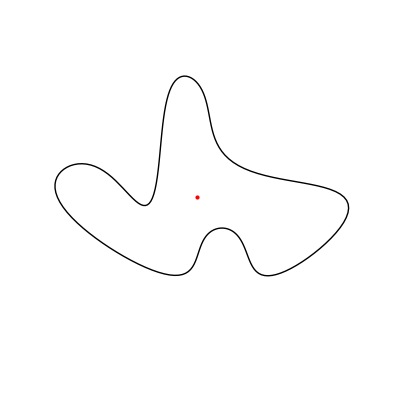
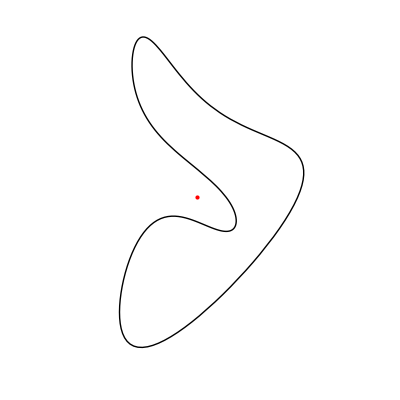
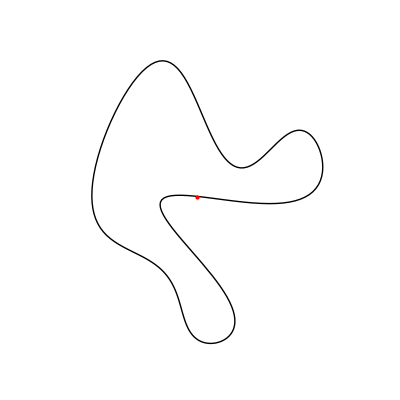
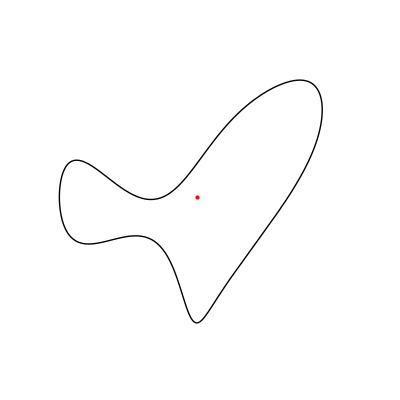
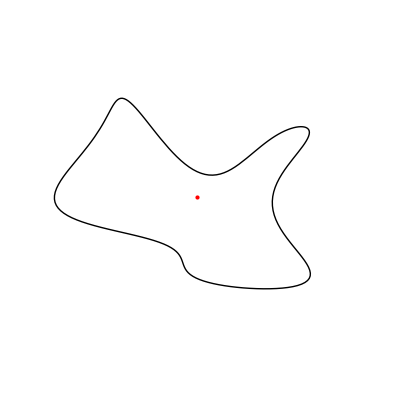
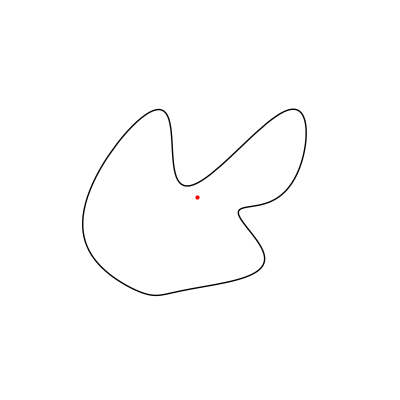
-Graphics-
E_1 | -Graphics-
E_2 | -Graphics-
E_3 | -Graphics-
E_4
-Graphics-
E_5 | -Graphics-
E_6 | -Graphics-
E_7 | -Graphics-
E_8
-Graphics-
E_9 | -Graphics-
E_10 | -Graphics-
E_11 | -Graphics-
E_12

```mathematica
iniplots=TableForm[Table[
Labeled[
ParametricPlot[Subscript[curve, 4(i-1)+j][u],{u,0,2π},PlotRange->{{-25,26},{-26,25}},AspectRatio->Full,Axes->False,PlotStyle->{Thick,Black},Epilog->{PointSize[Medium],Red,Point[{0,0}]},PerformanceGoal->"Speed"],Style[Subscript["E", 4(i-1)+j],22]] , {i,1,3},{j,1,4}]
];
```

```mathematica
evoplot2=evoplot3d[2,3,Boxed->False,PlotStyle->{{Black}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style[x,18],Style[y,18],Style[τ,18]},Ticks->{{0},{0},{{0,0},{100,T}}}];
```

-Graphics3D-

```mathematica
evoplot11=evoplot3d[11,3,Boxed->False,PlotStyle->{{Black}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style[x,18],Style[y,18],Style[τ,18]},Ticks->{{0},{0},{{0,0},{100,T}}}];
```

-Graphics3D-

```mathematica
evoplot12=evoplot3d[12,3,Boxed->False,PlotStyle->{{Black}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style[x,18],Style[y,18],Style[τ,18]},Ticks->{{0},{0},{{0,0},{100,T}}}];
```

-Graphics3D-

```mathematica
evocenplot12=cenplot3d[12,3,Boxed->False,PlotStyle->{{Black}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},AxesLabel->{Style[x,18],Style[y,18],Style[τ,18]},Ticks->{{0},{0},{{0,0},{100,T}}}];
```

-Graphics3D-

```mathematica
evocenplot2=cenplot3d[2,3,Boxed->False,PlotStyle->{{Black}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Ticks->{{0},{0},{{0,0},{100,T}}},ViewPoint->{1/3,-2,1/4},AxesLabel->{Style[x,18],Style[y,18],Style[τ,18]}];
```

-Graphics3D-

```mathematica
multicenplot=multicenplot3d[n,10,PlotRange->{{-90,90},{-90,90},{0,100}},AxesLabel->{Style[x,18],Style[y,18],Style[τ,18]},Ticks->{{0},{0},{{0,0},{100,T}}},AxesEdge->{{-1,-1},{1,-1},{-1,-1}}];
```

-Graphics3D-

```mathematica
Export["plots/PlotsInitialCurves.eps",iniplots];
Export["plots/Plot3DEvolution02.eps",evoplot2];
Export["plots/Plot3DEvolution11(wild).eps",evoplot11];
Export["plots/Plot3DEvolution12(wild).eps",evoplot12];
Export["plots/Plot3DEvolution02COMTrajectory.eps",evocenplot2];
Export["plots/Plot3DEvolution12COMTrajectory.eps",evocenplot2];
Export["plots/Plot3DCOMs.eps",multicenplot];
```

```mathematica
Clear[iniplots,evoplot2,evoplot11,evoplot12,evocenplot2,evocenplot12,multicenplot]
```

### renormalization group flow

#### pde

```mathematica
Block[{clist={0},noc,pde,bc,c},
noc=Length[clist];
z[t_]:=Sum[Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])],{num,clist}];
pde=Evaluate[D[z[t], t]] ==0;
bc=Sum[Subscript[l, num][t] Exp[-Subscript[iso, num][0](1+c[t]/Subscript[l, num][t])] /.t->0,{num,clist}]/z[0]==Sum[Subscript[l, num][t]/.t->0,{num,clist}]/noc;
Subscript[co, 0]=c[0]/.FindRoot[bc,{c[0],-290}];
Print[{noc,Subscript[co, 0]}];

Timing[Subscript[zsol, 0]=NDSolve[{pde,c[0]==Subscript[co, 0]},c,{t,0,99.9}]]//Print;
]
```

{1,-290.}

{0.012001,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

```mathematica
Do[zpde[i],{i,1,8}]
```

{3,-267.924}

{439.803,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

{4,-270.625}

{799.15,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

{5,-279.809}

{1275.08,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

{6,-279.904}

{1854.33,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

{7,-278.191}

{2561.07,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

{8,-275.937}

{3379.69,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

```mathematica
Do[zpde[i],{i,9,12}]
```

E9: c9(0)=-283.56

```mathematica
zpde[2]
```

E2: c2(0)=-267.7

$Aborted

#### saving solutions and interpolation functions for c(t)

```mathematica
Table[Subscript[zsol, i],{i,0,8}]>>cintfuns
```

```mathematica
Table[Subscript[solution, i],{i,0,8}]>>solintfuns
```

#### export data & plots

```mathematica
Export["table.c(0).dat",TableForm[Table[{i ,Subscript[co, i]},{i,0,8}]],"Data"];
```

```mathematica
Export["plots.coefficient.c(t)^2.eps",
TableForm[Table[c2plot[4(i-1)+j, AxesLabel -> {t, Superscript[Subscript[c, 4(i-1)+j][t],2]}],{i,1,2},{j,1,4}]
],"EPS"];
```

```mathematica
Export["plots.nonconformal_factor.(1+c_n(t)l_1(t)^(-)).eps",TableForm[Table[Plot[(1+(c[t]/.Subscript[zsol, 4(i-1)+j][[1]])/Subscript[l, 1][t]),{t,0,99.9},PlotRange->All,AxesLabel -> {t,StandardForm[1+ Subscript[c, 4(i-1)+j]/Subscript[l, 1]]}]
, {i,1,2},{j,1,4} ]]];
```

```mathematica
Export["plots.weights(N=8).e^(-S_i).eps",
TableForm[Table[ 
Plot[Exp[-action[8,4(i-1)+j,t]],{t,0,99.9},PlotRange->All,AxesLabel -> {t,StandardForm[Superscript[e,-Subscript[S, 4(i-1)+j][t]]]}]
, {i,1,2},{j,1,4} ]]];
```

```mathematica
Export["plots.weights(N=4).e^(-S_i).eps",
TableForm[{Table[ 
Plot[Exp[-action[4,j,t]],{t,0,99.9},PlotRange->All,AxesLabel -> {t,StandardForm[Superscript[e,-Subscript[S, j][t]]]}],{j,1,4} ]}
]];
```

```mathematica
Export["table.exponent_of_c(t).t_in_(91,100).eps",vtab[8,90.9,99.9]];
Export["table.exponent_of_c(t).t_in_(1,100).eps",vtab[8,0.9,99.9]];
```

```mathematica
Export["table.coefficient_of_c(t).t_in_(91,100).eps",ktab[8,90.9,99.9]];
Export["table.coefficient_of_c(t).t_in_(1,100).eps",ktab[8,0.9,99.9]];
```

#### centroid

```mathematica
mcplots=Block[{n=8},
ParametricPlot3D[
Table[Flatten[{ meancen[i,t],t/50}],{i,1,n}],{t,0,99},
PlotRange->All,PerformanceGoal->"Speed",MaxRecursion->1,
AxesLabel->{x,y,t/50}
]
]
```

-Graphics3D-

```mathematica
Export["plot3d.mean_centroid_trajectories.eps",mcplots,"EPS"];
```

```mathematica
Export["plot.mean_centroid_trajectory_projection.eps",meancenplot[8],"EPS"];
```

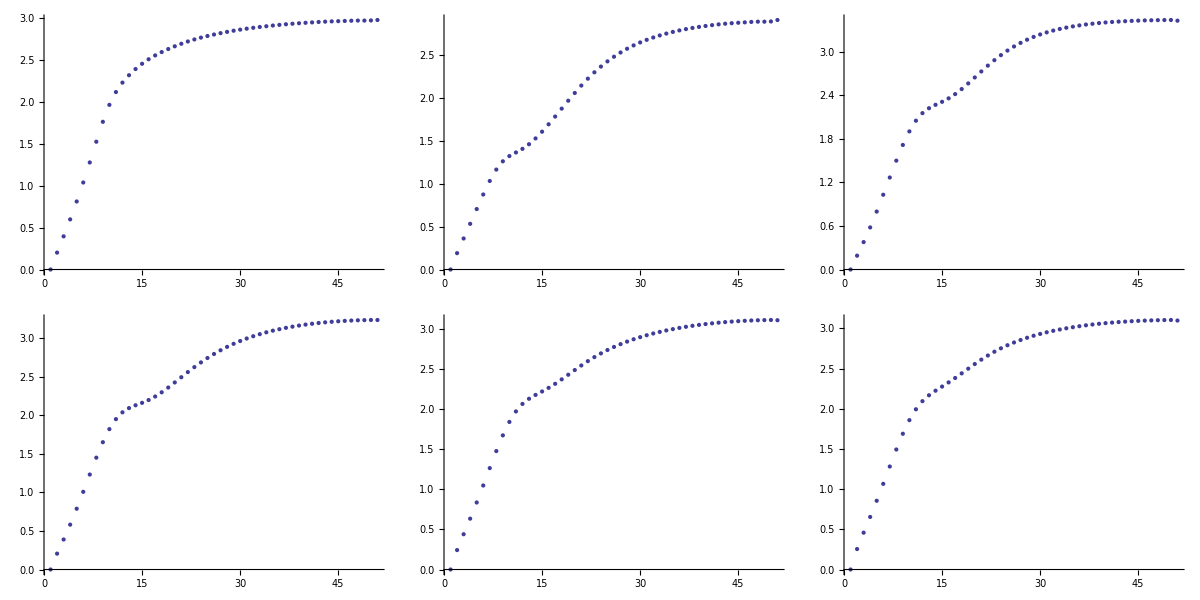

```mathematica
varplots=
TableForm[
Table[
ListPlot[Table[Norm@varcen[3i+j,99.9t/100],{t,0,100,2}],
PlotRange->All,PerformanceGoal->"Speed"
],{i,1,2},{j,0,2}]
]
```

```mathematica
Export["var.eps",varplots];
```

```mathematica
vartab=Block[{n=8,pts=99},
TableForm[
Table[Norm@varcen[i,99.9 j/pts],{j,0,pts},{i,2,n}
],TableHeadings->{Table[99.9 j/pts,{j,0,pts}],Range[2,n]}
]
]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8
0 | 5.464×10^-8 | 2.28613×10^-7 | 2.33383×10^-7 | 2.37435×10^-7 | 3.20741×10^-7 | 3.34637×10^-7 | 3.74012×10^-7
1.00909 | 0.124133 | 0.105022 | 0.101917 | 0.0997176 | 0.112525 | 0.134471 | 0.14162
2.01818 | 0.239893 | 0.203624 | 0.192474 | 0.192414 | 0.207932 | 0.244181 | 0.256627
3.02727 | 0.352095 | 0.301149 | 0.279417 | 0.285507 | 0.300145 | 0.345553 | 0.361639
4.03636 | 0.462775 | 0.400343 | 0.365574 | 0.381756 | 0.393446 | 0.443801 | 0.462154
5.04545 | 0.573281 | 0.501102 | 0.451526 | 0.481674 | 0.489066 | 0.541188 | 0.560839
6.05455 | 0.684693 | 0.604689 | 0.538004 | 0.585971 | 0.588222 | 0.639659 | 0.659866
7.06364 | 0.798001 | 0.711316 | 0.624954 | 0.694602 | 0.691166 | 0.740274 | 0.760529
8.07273 | 0.914258 | 0.82107 | 0.711976 | 0.807207 | 0.797741 | 0.843549 | 0.863525
9.08182 | 1.0347 | 0.934037 | 0.798356 | 0.92316 | 0.907457 | 0.949489 | 0.968993
10.0909 | 1.16078 | 1.05033 | 0.883051 | 1.04159 | 1.01952 | 1.05763 | 1.07657
11.1 | 1.29406 | 1.16999 | 0.964672 | 1.16139 | 1.13286 | 1.16701 | 1.18536
12.1091 | 1.43588 | 1.29275 | 1.04151 | 1.28125 | 1.24615 | 1.27664 | 1.29444
13.1182 | 1.58685 | 1.41764 | 1.11168 | 1.39972 | 1.35788 | 1.38492 | 1.40227
14.1273 | 1.74625 | 1.54276 | 1.17344 | 1.5153 | 1.46643 | 1.49034 | 1.50741
15.1364 | 1.91152 | 1.66515 | 1.22559 | 1.62642 | 1.5701 | 1.59129 | 1.60834
16.1455 | 2.07821 | 1.78121 | 1.26785 | 1.73148 | 1.6672 | 1.68619 | 1.70356
17.1545 | 2.24062 | 1.8874 | 1.30108 | 1.82887 | 1.75611 | 1.77357 | 1.79174
18.1636 | 2.39312 | 1.9813 | 1.3272 | 1.91707 | 1.83547 | 1.8522 | 1.87176
19.1727 | 2.53156 | 2.06222 | 1.34883 | 1.9949 | 1.90433 | 1.92129 | 1.94291
20.1818 | 2.6541 | 2.13119 | 1.36876 | 2.06164 | 1.9623 | 1.98057 | 2.00495
21.1909 | 2.76097 | 2.19025 | 1.38938 | 2.11726 | 2.00966 | 2.03036 | 2.05818
22.2 | 2.85369 | 2.24168 | 1.41236 | 2.16244 | 2.04735 | 2.07156 | 2.10345
23.2091 | 2.93422 | 2.28739 | 1.43865 | 2.1986 | 2.07686 | 2.10552 | 2.14187
24.2182 | 3.00446 | 2.32879 | 1.46859 | 2.22782 | 2.10012 | 2.13402 | 2.17507
25.2273 | 3.06599 | 2.36675 | 1.502 | 2.252 | 2.11902 | 2.1586 | 2.2044
26.2364 | 3.12011 | 2.40176 | 1.53857 | 2.27346 | 2.13556 | 2.18098 | 2.23137
27.2455 | 3.16783 | 2.43411 | 1.57781 | 2.29417 | 2.15142 | 2.20253 | 2.25722
28.2545 | 3.21001 | 2.46397 | 1.61924 | 2.31567 | 2.16789 | 2.22428 | 2.28286
29.2636 | 3.24736 | 2.49152 | 1.66241 | 2.33909 | 2.18592 | 2.24692 | 2.30891
30.2727 | 3.28048 | 2.51695 | 1.70691 | 2.36512 | 2.20607 | 2.2708 | 2.33567
31.2818 | 3.3099 | 2.54047 | 1.75241 | 2.39408 | 2.22861 | 2.29607 | 2.36327
32.2909 | 3.33609 | 2.56233 | 1.79861 | 2.42599 | 2.25358 | 2.32265 | 2.39165
33.3 | 3.35944 | 2.58278 | 1.84525 | 2.46066 | 2.28084 | 2.35037 | 2.42065
34.3091 | 3.38029 | 2.60205 | 1.89206 | 2.49773 | 2.31013 | 2.37897 | 2.45006
35.3182 | 3.39894 | 2.62033 | 1.93878 | 2.53675 | 2.34113 | 2.40817 | 2.47961
36.3273 | 3.41566 | 2.63777 | 1.98514 | 2.57724 | 2.37347 | 2.43766 | 2.50907
37.3364 | 3.43067 | 2.65446 | 2.03088 | 2.61866 | 2.40677 | 2.46716 | 2.5382
38.3455 | 3.44416 | 2.67043 | 2.07574 | 2.66052 | 2.44069 | 2.49643 | 2.56678
39.3545 | 3.4563 | 2.68572 | 2.11945 | 2.70235 | 2.47486 | 2.52523 | 2.59463
40.3636 | 3.46723 | 2.7003 | 2.16182 | 2.74374 | 2.509 | 2.55338 | 2.62161
41.3727 | 3.47709 | 2.71415 | 2.20266 | 2.78433 | 2.54285 | 2.58073 | 2.6476
42.3818 | 3.486 | 2.72726 | 2.24186 | 2.82385 | 2.57618 | 2.60718 | 2.67252
43.3909 | 3.49405 | 2.73963 | 2.27933 | 2.86206 | 2.60882 | 2.63264 | 2.69632
44.4 | 3.50134 | 2.75129 | 2.31504 | 2.8988 | 2.64064 | 2.65707 | 2.71899
45.4091 | 3.50794 | 2.76227 | 2.34901 | 2.93395 | 2.67152 | 2.68046 | 2.74051
46.4182 | 3.51394 | 2.77263 | 2.38127 | 2.96744 | 2.70139 | 2.70281 | 2.76092
47.4273 | 3.51938 | 2.78244 | 2.41188 | 2.99923 | 2.7302 | 2.72413 | 2.78026
48.4364 | 3.52431 | 2.79176 | 2.44092 | 3.02931 | 2.75791 | 2.74445 | 2.79856
49.4455 | 3.5288 | 2.80067 | 2.46845 | 3.05769 | 2.78449 | 2.76378 | 2.81587
50.4545 | 3.53286 | 2.80921 | 2.49455 | 3.08441 | 2.80994 | 2.78225 | 2.8323
51.4636 | 3.53655 | 2.81744 | 2.51926 | 3.1095 | 2.83427 | 2.79985 | 2.84787
52.4727 | 3.5399 | 2.82538 | 2.54263 | 3.13303 | 2.85748 | 2.81662 | 2.86265
53.4818 | 3.54293 | 2.83304 | 2.56472 | 3.15505 | 2.87961 | 2.83262 | 2.87668
54.4909 | 3.54568 | 2.84041 | 2.58556 | 3.17572 | 2.90075 | 2.84794 | 2.89005
55.5 | 3.54817 | 2.84749 | 2.60519 | 3.19495 | 2.9208 | 2.86248 | 2.90269
56.5091 | 3.55042 | 2.85426 | 2.62367 | 3.21291 | 2.93988 | 2.87636 | 2.91469
57.5182 | 3.55246 | 2.86071 | 2.64103 | 3.22966 | 2.95802 | 2.88959 | 2.92608
58.5273 | 3.55431 | 2.86683 | 2.65734 | 3.24529 | 2.97527 | 2.90221 | 2.93687
59.5364 | 3.55598 | 2.87264 | 2.67268 | 3.25984 | 2.99167 | 2.91424 | 2.94709
60.5455 | 3.55748 | 2.87815 | 2.6871 | 3.2734 | 3.00726 | 2.9257 | 2.95677
61.5545 | 3.55884 | 2.8834 | 2.70068 | 3.28602 | 3.02207 | 2.93663 | 2.96593
62.5636 | 3.56007 | 2.8884 | 2.7135 | 3.29776 | 3.03613 | 2.94705 | 2.97461
63.5727 | 3.56116 | 2.89321 | 2.72561 | 3.30867 | 3.04947 | 2.95699 | 2.98284
64.5818 | 3.56214 | 2.89784 | 2.73708 | 3.31881 | 3.06212 | 2.96647 | 2.99065
65.5909 | 3.56302 | 2.90234 | 2.74794 | 3.32823 | 3.07411 | 2.97553 | 2.99809
66.6 | 3.56379 | 2.90671 | 2.75822 | 3.33699 | 3.08547 | 2.98418 | 3.00518
67.6091 | 3.56448 | 2.91096 | 2.76796 | 3.34513 | 3.09622 | 2.99245 | 3.01195
68.6182 | 3.56508 | 2.91507 | 2.77714 | 3.35271 | 3.10639 | 3.00034 | 3.01838
69.6273 | 3.56561 | 2.91904 | 2.7858 | 3.35976 | 3.11603 | 3.00791 | 3.02456
70.6364 | 3.56607 | 2.92284 | 2.79393 | 3.36634 | 3.12517 | 3.01514 | 3.03045
71.6455 | 3.56648 | 2.92644 | 2.80156 | 3.37247 | 3.13383 | 3.02205 | 3.03606
72.6545 | 3.56683 | 2.92985 | 2.80871 | 3.37819 | 3.14204 | 3.02864 | 3.04138
73.6636 | 3.56714 | 2.93305 | 2.81542 | 3.38351 | 3.14983 | 3.03491 | 3.04641
74.6727 | 3.5674 | 2.93607 | 2.82173 | 3.38845 | 3.15721 | 3.04086 | 3.05116
75.6818 | 3.56763 | 2.93892 | 2.8277 | 3.39303 | 3.1642 | 3.04651 | 3.05561
76.6909 | 3.56782 | 2.94164 | 2.83337 | 3.39726 | 3.17081 | 3.05186 | 3.0598
77.7 | 3.56799 | 2.94426 | 2.83879 | 3.40116 | 3.17704 | 3.05692 | 3.06373
78.7091 | 3.56813 | 2.94682 | 2.84398 | 3.40474 | 3.18291 | 3.06171 | 3.06744
79.7182 | 3.56824 | 2.94932 | 2.84893 | 3.40805 | 3.18841 | 3.06624 | 3.07095
80.7273 | 3.56833 | 2.95175 | 2.85362 | 3.41109 | 3.19356 | 3.07052 | 3.07427
81.7364 | 3.56841 | 2.9541 | 2.85803 | 3.41391 | 3.19836 | 3.07457 | 3.07743
82.7455 | 3.56847 | 2.95631 | 2.8621 | 3.41653 | 3.20284 | 3.0784 | 3.08044
83.7545 | 3.56851 | 2.95834 | 2.86579 | 3.41896 | 3.20701 | 3.08199 | 3.08328
84.7636 | 3.56855 | 2.96015 | 2.86909 | 3.42124 | 3.2109 | 3.08536 | 3.08595
85.7727 | 3.56858 | 2.96173 | 2.87203 | 3.42334 | 3.21451 | 3.08849 | 3.08841
86.7818 | 3.5686 | 2.96311 | 2.87468 | 3.42526 | 3.21787 | 3.09138 | 3.09066
87.7909 | 3.56861 | 2.96437 | 2.87716 | 3.42699 | 3.22097 | 3.09402 | 3.09267
88.8 | 3.56863 | 2.96558 | 2.87958 | 3.42851 | 3.22384 | 3.09643 | 3.09446
89.8091 | 3.56864 | 2.96686 | 2.88204 | 3.42982 | 3.22645 | 3.09862 | 3.09606
90.8182 | 3.56864 | 2.96823 | 2.88454 | 3.43094 | 3.22879 | 3.1006 | 3.0975
91.8273 | 3.56864 | 2.96961 | 2.88695 | 3.4319 | 3.23086 | 3.10238 | 3.09882
92.8364 | 3.56864 | 2.97086 | 2.88899 | 3.43279 | 3.23266 | 3.10399 | 3.10006
93.8455 | 3.56864 | 2.97168 | 2.8903 | 3.43364 | 3.23416 | 3.10539 | 3.10122
94.8545 | 3.56864 | 2.97184 | 2.89062 | 3.43449 | 3.23538 | 3.10656 | 3.10225
95.8636 | 3.56862 | 2.97141 | 2.89014 | 3.43529 | 3.23634 | 3.10747 | 3.10308
96.8727 | 3.56859 | 2.97109 | 2.88994 | 3.43583 | 3.23712 | 3.10815 | 3.10361
97.8818 | 3.56896 | 2.97284 | 2.89267 | 3.43594 | 3.23813 | 3.10882 | 3.10384
98.8909 | 3.56869 | 2.9782 | 2.90159 | 3.43471 | 3.23965 | 3.1094 | 3.10318
99.9 | 3.55597 | 2.97855 | 2.90975 | 3.4267 | 3.23808 | 3.10601 | 3.09723

```mathematica
Export["table.variance_of_centroids.var(n,t).eps",vartab];
```

#### !! caution: read in of data !!

```mathematica
Block[{n=8,zsoltab},
zsoltab =<<DataCInterpolatingFunctions;
Do[Subscript[zsol, num]=zsoltab[[num+1,1]],{num,1,n}];
TableForm@Table[Subscript[zsol, num],{num,1,8}]
]
```

c→InterpolatingFunction[{{0.,99.9}},<>]
c→InterpolatingFunction[{{0.,99.9}},<>]
c→InterpolatingFunction[{{0.,99.9}},<>]
c→InterpolatingFunction[{{0.,99.9}},<>]
c→InterpolatingFunction[{{0.,99.9}},<>]
c→InterpolatingFunction[{{0.,99.9}},<>]
c→InterpolatingFunction[{{0.,99.9}},<>]
c→InterpolatingFunction[{{0.,99.9}},<>]

#### plots

```mathematica
z[n_,t_]:=Sum[Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])],{num,1,n}]
```

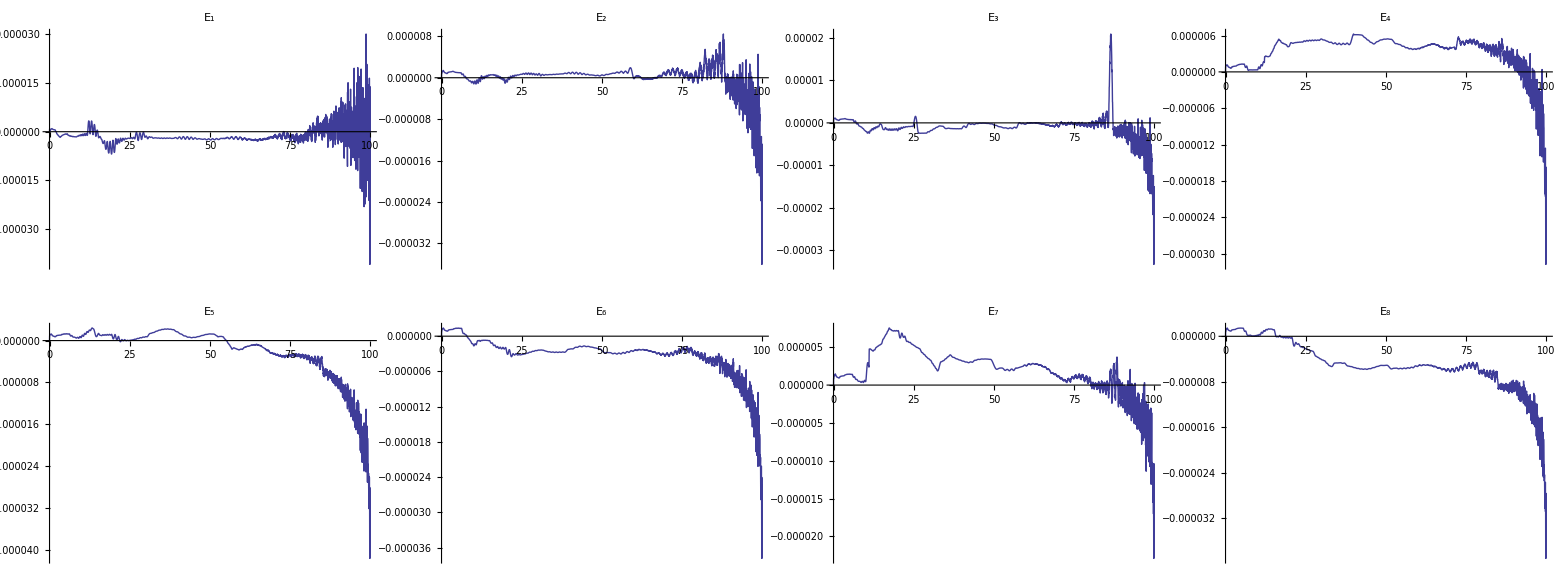

```mathematica
TableForm[Table[Plot[-1+z[num,t]/z[num,0]/. Subscript[zsol, num],{t,0,99.9},PlotLabel->Subscript["E", num],PlotRange->All],{ii,1,2},{num,4(ii-1)+1,4(ii-1)+4}]]
```

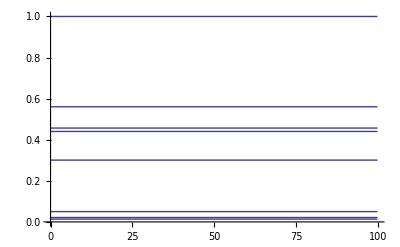

```mathematica
Block[{normfac},
normfac=z[1,0]/. Subscript[zsol, 1];
Plot[Table[z[num,t]/normfac/. Subscript[zsol, num],{num,1,8}],{t,0,99.9},PerformanceGoal->"Speed"]
]
```

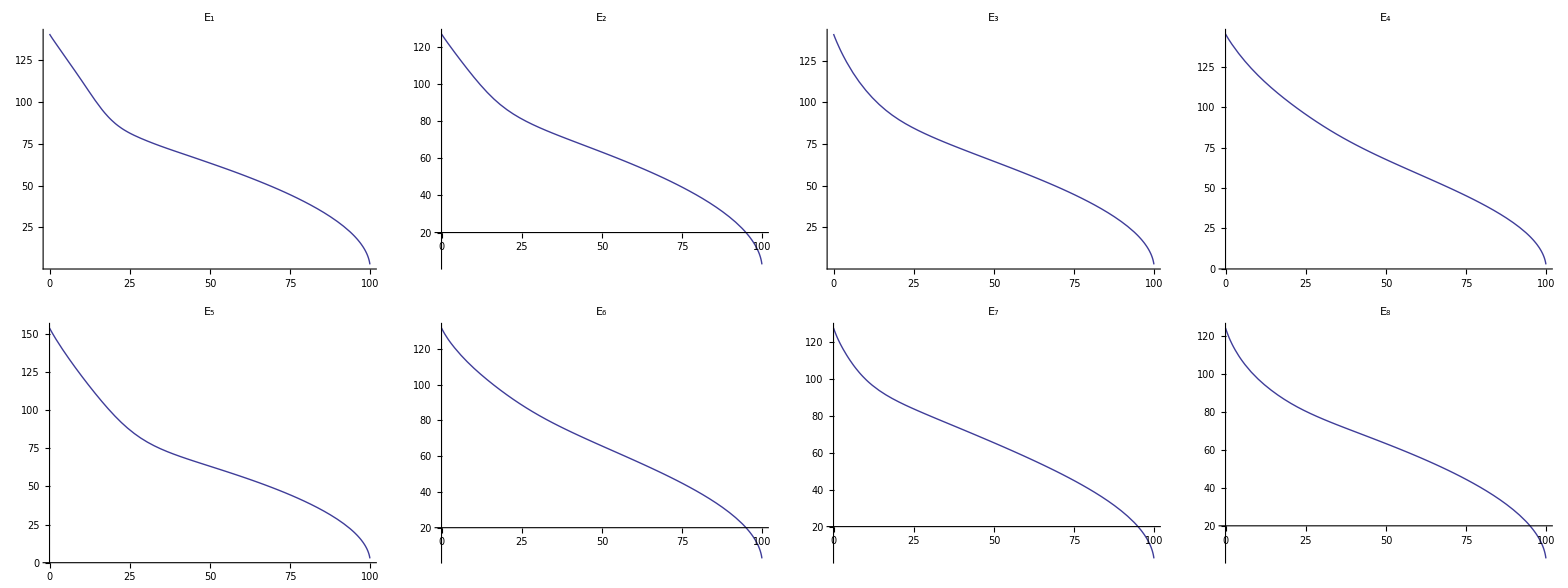

```mathematica
TableForm[Table[Plot[Subscript[l, num][t],{t,0,99.9},PlotLabel->Subscript["E", num],PlotRange->All],{ii,1,2},{num,4(ii-1)+1,4(ii-1)+4}]]
```

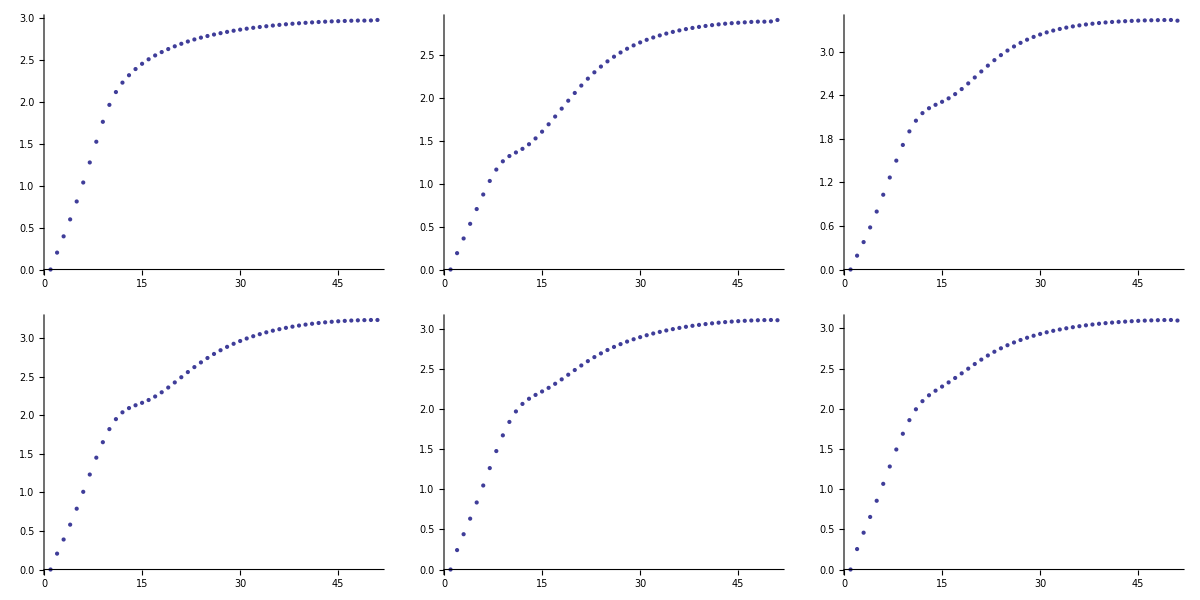

```mathematica
TableForm[
Table[
ListPlot[Table[Norm@varcen[3i+j,99.9t/100],{t,0,100,2}],
PlotRange->All,PerformanceGoal->"Speed"
],{i,1,2},{j,0,2}]
]
```

#### buffer

```mathematica
Block[{x=Subscript[curve, 1,1][u][[1]],y=Subscript[curve, 1,1][u][[2]]},NIntegrate[1/2 (x D[y, u] - y D[x, u]),{u,0,2π}]]
```

```mathematica
Block[{num=0,c,X,Y,n,grd,ugrid,fddf},
c[u_]:={Sin[u],Cos[u]};
n=200;
grd=Range[0,n];
ugrid=2π grd /n;
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1],grd ,DifferenceOrder -> 4];
X=Map[c, ugrid][[All,1]];
Y=Map[c, ugrid][[All,2]];
Total@fddf[Thread[Subscript[x, grd]]];
N@Total[Drop[Sqrt[fddf[X]^2+fddf[Y]^2],1]]
] - 2Pi
```

-2.03989×10^-7